```mathematica
l=4;
tryit=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}]
FullSimplify[Abs[Sin[h]]*LegendreQ[l,1,Cos[h]],{h>0}];
god=D[tryit,h]/Sin[h];
Series[god,{h,0,1}];
(*Plot[tryit,{h,0,Pi}]
Plot[god,{h,0,Pi}]*)
```

-5/4 Cos[h] (1+7 Cos[2 h]) Sin[h]^2

InterpolatingFunction[{{0.00552428,1.563}},<>]

InterpolatingFunction[{{0.00552428,1.563}},<>]

InterpolatingFunction[{{0.00552428,1.563}},<>]

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

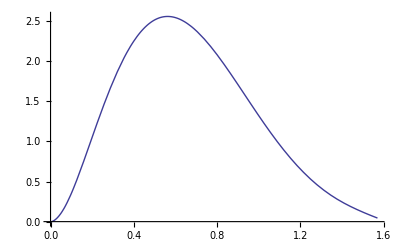

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

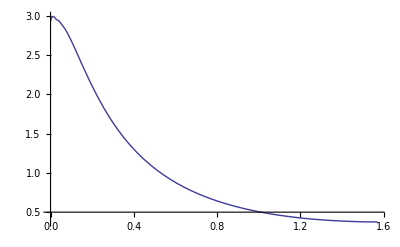

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

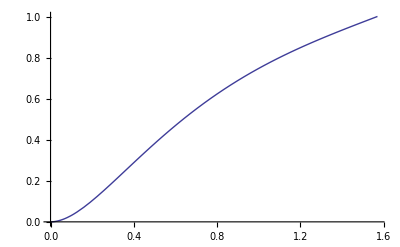

```mathematica
lst=ReadList[NotebookDirectory[]<>"aphi0.9999.txt",Number,RecordLists->True];
lsttran=Transpose[lst];
hlist=lsttran[[1]];
aphilist=lsttran[[2]];
residlist=lsttran[[3]];
brlist=lsttran[[4]];
haphilist=Partition[Riffle[hlist,aphilist],2];
hresidlist=Partition[Riffle[hlist,residlist],2];
hbrlist=Partition[Riffle[hlist,brlist],2];
aphinum=Interpolation[haphilist]
residnum=Interpolation[hresidlist]
brnum=Interpolation[hbrlist]
Plot[residnum[h],{h,0,Pi/2}]
Plot[brnum[h],{h,0,Pi/2}]
Plot[aphinum[h],{h,0,Pi/2}]
```

```mathematica
aphinum[h]/.h->1
```

aphilist

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

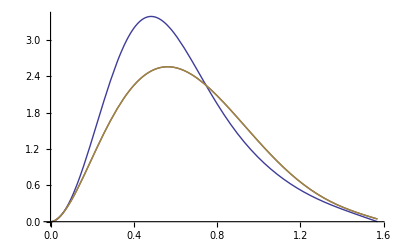

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::ivar: 0.0000320891 is not a valid variable.

General::ivar: 0.0320892 is not a valid variable.

General::ivar: 0.0641462 is not a valid variable.

General::stop: Further output of General will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.5707962947378287`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

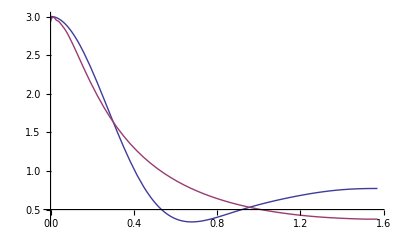

```mathematica
(* QUADRUPOLAR EXPANSION *)
(* Weight of quadrupolar Jon's term *)
ac=0.1;
a=0.9999;
aphi4Jon:=6.5(ac*5/4 Cos[h] (1+7 Cos[2 h]) Sin[h]^2+(1-ac)Sin[h]^2*Cos[h]);
(* SASHA'S BY-EYE FIT *)
pow1=10;
pow2=5;
pow4=3.5;
coef2=0.2;
coef3=0.05;
coef4=0.2;
coef1=1.7-coef2-coef3-coef4;
aphi4:=(24*Sin[h]^2*(coef1*Cos[h]^pow1+coef2*Cos[h]^pow2+coef4*Cos[h]^pow4+coef3*Cos[h]^1))
Plot[{aphi4,residnum[h],(aphinum[h]-aphi0-aphi2)/omh^4},{h,0,Pi/2}]
(* COMPUTE B^r *)
rh=1+Sqrt[1-a^2];
omh=a/(2rh);
sigma=rh^2+a^2 Cos[h]^2;
aphi0=1-Cos[h];
aphi2=(2*(-49+6*Pi^2))/9.*omh^2*Sin[h]^2*Cos[h];
aphi=aphi0+omh^2*aphi2+omh^4*aphi4;
aphiJon=aphi0+omh^2*aphi2+omh^4*aphi4Jon;
gdet=sigma Sin[h];
Br=D[aphi,h]/gdet;
Brnum[h_]:=D[aphinum[h],h]/gdet;
BrJon=D[aphiJon,h]/gdet;
Plot[{Br,brnum[h],Brnum[h]},{h,0,Pi/2},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

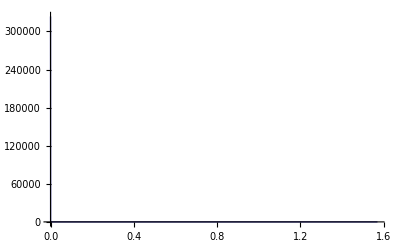

```mathematica
Plot[Brnum,{h,0,Pi/2},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

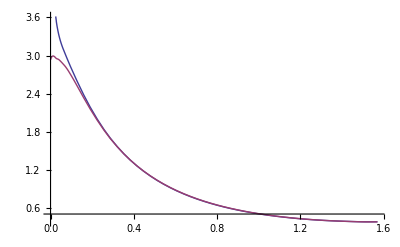

```mathematica
Plot[{aphinum'[h]/gdet,brnum[h]},{h,0,Pi/2}]
```